```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
number=3;
luminosity = 5 (*fb^-1*);
crossection={951.064,930.127,906.368 ,882.925,859,733}; (*fb*)
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =IntegerPart[numbevents[[number]]]
npseudobin=20;
pvaluestandard=0.0455;
numbofdiffdist=4;
```

18127

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])"};varnorm=Table["1/σ"<>ToString[(variable[[i]]/dσ),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","deltaRb1b2","deltaRe+mu-","deltaRe+b1","deltaRe+b2","deltaRmu-b1","deltaRmu-b2","deltaRttbar"};
```

```mathematica
DATA FROM HELAC;
```

```mathematica
file=Table[FileNames[][[i]],{i,1,Length[mass]}];
nbins=20;

start[n_]:=2+(n-1)*20
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,Length[mass],1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,Length[mass],1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,1]]],{i,1,Length[mass],1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,5}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,Length[mass],1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,Length[mass],1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,Length[mass]}];
factor=Table[Sum[vals[[j,i]],{i,1,20,1}]*bwreal[[j]]*10^-3,{j,1,Length[mass]}]; (*area under the histogram*)

vals=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,Length[mass],1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnorm=Table[vals[[i]]/factor[[i]],{i,1,Length[mass]}];(*normalised differential distribution : divided by 1/cross section *)

counts=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,Length[mass],1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
countsmax=Table[Sum[counts[[i,j]],{j,1,Length[counts[[i]]]}],{i,1,Length[mass]}];
countsnorm=Table[counts[[i]]/countsmax[[i]],{i,1,Length[mass]}];

error=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,Length[mass],1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnorm=Table[error[[i]]/factor[[i]],{i,1,Length[mass]}];
```

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)
wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[bins[[i]],counts[[i]]]],{i,1,Length[mass],1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsreal[[i]]],Max[binsreal[[i]]],bwreal[[i]]}]],{i,1, Length[mass],1}]][[2,1]]
];
```

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
ratio=Block[{maxcount,posmax,rat},
maxcount= Reap[Do[Sow[Max[countsnorm[[i]]]],{i,1,Length[mass],1}]][[2,1]];
posmax=Reap[Do[Sow[Flatten[Position[countsnorm[[i]],maxcount[[i]]]]],{i,1,Length[mass],1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(valsnorm[[i,posmax[[i]]]]*bwreal[[i]])/countsnorm[[i,posmax[[i]]]]],{i,1,Length[mass],1}]][[2,1]]]
];
```

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_]:=HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw][[1]],Max[histogramlistnorm[nevents,nmass,binw][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_]:=histogramlistnorm[nevents,nmass,binw][[2]]*ratio[[nmass]]/binw (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_]:=MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw],pseudopointy[nevents,nmass,binw]}]

pseudoerror[nevents_,nmass_,binw_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw][[2,i]]]]/nevents]*ratio[[nmass]]/binw],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_]:=Transpose[{pseudodata[nevents,nmass,binw][[All,1]],pseudodata[nevents,nmass,binw][[All,2]],pseudoerror[nevents,nmass,binw]}]
pseudoplot[nevents_,nmass_,binw_]:=ErrorListPlot[pseudo[nevents,nmass,binw],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]
```

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
```

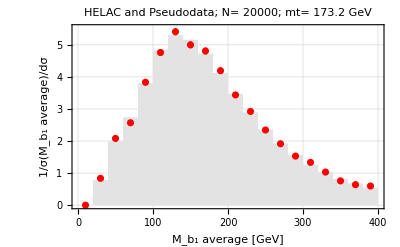

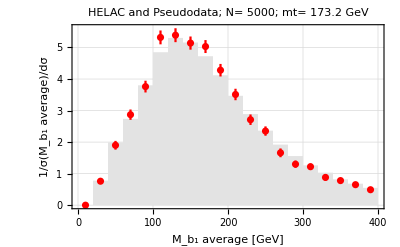

```mathematica
binhelac=bins;
valhelac=valsnorm;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsreal;

histfromhelac[nmass_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]}]

combine[nevents_,nmass_,binw_]:=Show[histfromhelac[nmass],pseudoplot[nevents,nmass,binw],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]
pt1=combine[20000,3,(binwidth[[1]]*nbins/npseudobin)]
pt2=combine[5000,3,(binwidth[[1]]*nbins/npseudobin)]
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormtheo=Reap[Do[Sow[valsnorm[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidth[[1]]*nbins/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errnorm[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidth[[1]]*nbins/npseudobin);

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,Length[mass],1}]][[2,1]]; (*for graph*)
valsbindatanozero=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,Length[mass]}];
Sow[DeleteCases[valerr,nol]]]][[1]];

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,Length[mass],1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,Length[mass]}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];
```

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,Length[mass],1},{j,1,nbins,1}]
][[2]];
all=Flatten[Table[{Range[Length[mass]][[i]],Range[nbins][[j]]},{i,1,Length[mass]},{j,1,nbins}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20}}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value=Reap[Do[Sow[valsbintheonozero[[i]][[All,1]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
err=Reap[Do[Sow[valsbintheonozero[[i]][[All,2]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];

fitting=LinearModelFit[value[[#]],{x,x^2},x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]];
```

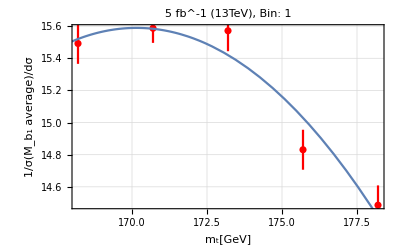
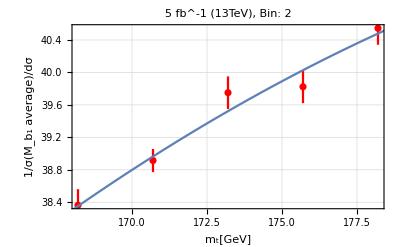
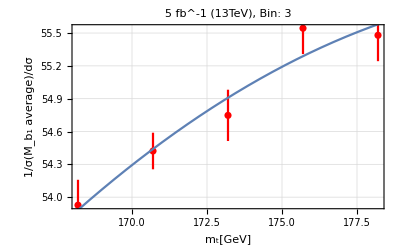
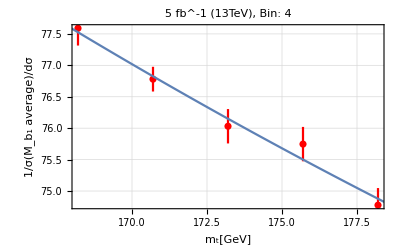
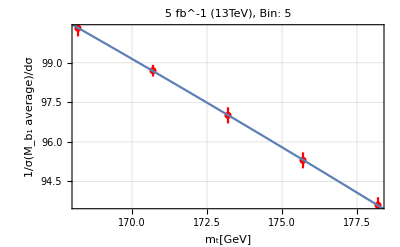
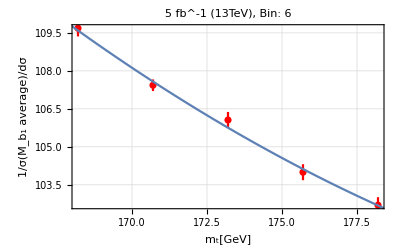
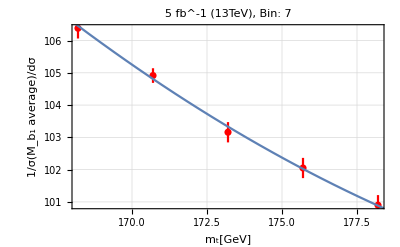
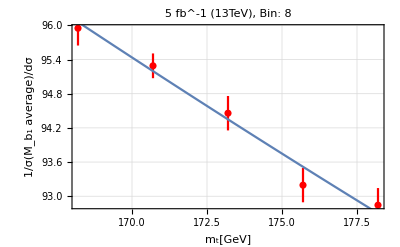

```mathematica
valsbinplot[int_]:=ErrorListPlot[valsbindatanozero[[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_]:=Normal[fitting[[int]]]
funcbin[int_,nmass_]:=funcfit[int]/.x-> mass[[nmass]]
combbinfunc[int_]:=Block[{func},
func=funcfit[int]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit=Table[combbinfunc[i],{i,1,Length[value]}]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormpseudo[nevents_]:=Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,Length[mass],1}]][[2,1]];
Which[MemberQ[nonzerobin, Nothing]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]] (*length value=non zero bins total*)
]
]
]
errnormpseudo[nevents_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,Length[mass],1}]][[2,1]];
Which[MemberQ[nonzerobin, Nothing]==True,errpseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]]
]
]
]

PSEUDODATA USED FOR GENERATING THE CHISQUARE;
valuep=valsnormpseudo[20000][[3]];
errorp=errnormpseudo[20000][[3]] ;(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)
```

```mathematica
THE χ^2 PROCEDURE;
```

171.353

171.398

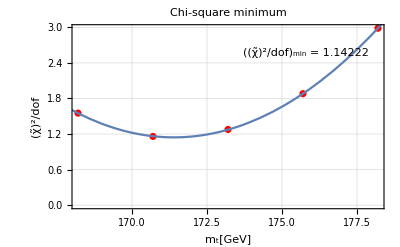

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_]:=(pvalue[[int]]-fitting[[int]][mass])^2/(perror[[int]]^2);
sumchisquare[pvalue_,perror_,mass_]:=Sum[chisquarebin[pvalue,perror,i,mass],{i,1,Length[pvalue]-1}];
chitilde[pvalue_,perror_,mass_]:=sumchisquare[pvalue,perror,mass]/(Length[pvalue]-1)
minchitilde[pvalue_,perror_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x],{x,162.8,178.2}]]
chidata=Table[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]]],{i,1,5}][[j]]},{j,1,Length[mass]}];
chifunc=Fit[chidata,{1,x,x^2},x];
minimumx=minchitilde[valuep,errorp]
x/.Last[FindMinimum[chifunc,{x,168.2}]]
chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[chifunc,{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["\n ((χ̃)^2/dof)_min = " <> ToString[chitilde[valuep,errorp,minimumx]]],Background->White],Scaled[{.75,.85}]]]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,n_]:=Partition[Reap[Do[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,datachi,fchi,mout,chisqmin,result},
pvaluelist=valsnormpseudo[nevents][[m]];
perrorlist=errnormpseudo[nevents][[m]];
datachi=Reap[Do[Sow[{mass[[j]],Reap[Do[Sow[chitilde[pvaluelist,perrorlist,mass[[i]]]],{i,1,5}]][[2,1]][[j]]}],{j,1,Length[mass]}]][[2,1]];
fchi=Fit[datachi,{1,x,x^2},x];
mout=minchitilde[pvaluelist,perrorlist];
chisqmin=chitilde[pvaluelist,perrorlist,mout];
result=Sow[{mout,chisqmin}]
]
];
,{m,1,Length[mass],1}]][[2,1]],n];
exp=npseudoexp[20000,100];
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

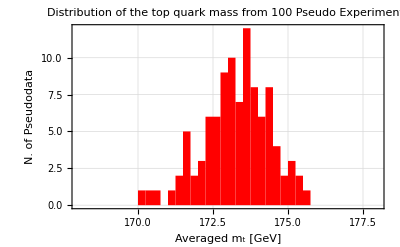

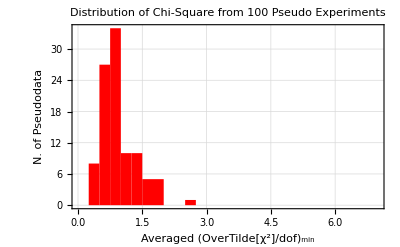

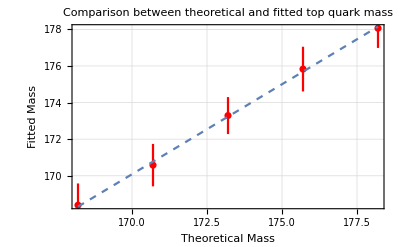

Theory, LO QCD | Variable | m_t±δm_t | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=E_T/2 | M_b_1 average | 173.289±1.01019 | 0.948343 | 0.481715 | -0.0887206

```mathematica
pexpmass=exp[[3]][[All,1]];
pexpchisq=exp[[3]][[All,2]];

massout=Table[Mean[exp[[i]][[All,1]]],{i,1,Length[exp]}];
(*deltamassout=Table[StandardDeviation[exp[[i]][[All,1]]],{i,1,Length[exp]}]*)
deltamassout=Reap[Do[Block[{sortedmass,variance},
sortedmass=exp[[m]][[All,1]];
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]
,{m,1,Length[mass]}]][[2,1]];
chiout=Table[Mean[exp[[i]][[All,2]]],{i,1,Length[exp]}];

pexpmasshist=Histogram[pexpmass,{168,178,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from 100 Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchisq,{0,7,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from 100 Pseudo Experiments"]

fitmassplot=ErrorListPlot[Table[{{mass[[i]],massout[[i]]},ErrorBar[deltamassout[[i]]]},{i,1,Length[mass]}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],massout[[i]]},{i,1,Length[mass]}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout[[3]]*(Length[pvalue]-1),Length[pvalue]-1][[2]];
pvout=pvalue[valuep];
pvout>pvaluestandard;
avechidof=chiout[[3]];
deltam=mass[[3]]-massout[[3]];
result=Grid[{{"Theory, LO QCD", "Variable",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm], "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{"Full, μ_0=E_T/2",variable[[numbofdiffdist]],PlusMinus[massout[[3]],deltamassout[[3]]],avechidof,pvout,deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
Export[varname[[numbofdiffdist]]<>"_pseudodata_20000.pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_pseudodata_5000.pdf",pt2];
Export[varname[[numbofdiffdist]]<>"_pseudo_vs_theo_each_bin.pdf",allfit];
Export[varname[[numbofdiffdist]]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_mass fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_result_table.pdf", result];
```